# Linkage map construction in multiparental populations

## Chaozhi Zheng Wageningen University and Research 30 August 2018

## Outlines

Selection mapping population

Simulate genomic data

Map construction

Compare with true map

## Load MagicMap

First set directory to the directory of the Mathematica packages.
Then load the package by functions Needs or Get. 
Use  the directory of the current notebook as the work directory.

```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"RABBIT_Packages"}]];
Get["MagicMap`"]
myParallelNeeds["MagicMap`"]
SetDirectory[NotebookDirectory[]]
```

D:\Chaozhi\DirectoryWUR\RABBIT Software\RABBIT_Tutorial

Get help information on functions or options by ?

```mathematica
?"MagicMap`*"
?graphLaplacian
```

graphLaplacian is an option to specify one of three graph Laplacians: "unNormalized","rwNormalized",or "symNormalized".

## Select an example population

```mathematica
codels={"f2","2wayril-self6","cp","4wayril-self4"}; popcode=codels[[1]];
pedls=Table[pedigree=compilePopPedigree[codels[[i]]];
Column[{"popcode = "<>codels[[i]],pedigreePlot[pedigree,ImageSize->Switch[i,1|2,100,_,200]]}],{i,Length[codels]}];
TabView[Transpose[{codels,Thread[{"F2","2-way RIL","CP","4-way RIL"}->pedls]}],Dynamic[popcode],ImageSize->Automatic]
```

f22wayril-self6cp4wayril-self4

## Simulate genomic data

```mathematica
popsize=100; Print["population code = ", popcode];
simpedinforfile=simPedigreeInfor[popcode,sampleSize->popsize,outputFileID->"Example"];
isfounderinbred=popcode=!="cp";
datafiles=magicGeneDropping["Arabidopsis_MAGIC_19FounderHaplo.csv",simpedinforfile,dropMonomorphic->True,outputFileID->"Example",isFounderInbred->isfounderinbred,founderGenotypeMissing->0.1,offspringGenotypeMissing->0.1,offspringAllelicError->0.05,isPrintTimeElapsed->True];
```

population code = f2

magicGeneDropping. Start date = Thu 30 Aug 2018 16:03:07

Time elapsed = 0. Seconds. 	Start simulating offspring genomes in terms of FGL lists.

Time elapsed = 1. Seconds. 	Start dropping founder alleles on the offspring FGL lists.

Time elapsed = 1.4 Seconds. 	Start simulating allelic errors in founders and offspring.

The realized fraction of missing genotypes in founders: 0.114

The realized fraction of missing genotypes in offspring: 0.1

Saving true values and simulated data. Thu 30 Aug 2018 16:03:09
	True FGL | Example_TrueValues_Fgl.txt
True FGL diplotype | Example_TrueValues_FglDiplotype.csv
True diplotype | Example_TrueValues_Diplotype.csv
Observed genotype | Example_ObservedGenotype.csv

Done! Finished date =Thu 30 Aug 2018 16:03:09. 	Time elapsed = 1.9 Seconds.

## Map construction

```mathematica
Options[magicMap]
```

{founderAllelicError→0.005,offspringAllelicError→0.005,isFounderInbred→True,computingLodType→both,sequenceDataOption→{isFounderAllelicDepth→Automatic,isOffspringAllelicDepth→Automatic,minPhredQualScore→30,priorFounderCallThreshold→0.99},outputFileID→,isPrintTimeElapsed→True,isRunInParallel→True,minLodSaving→1,miniComponentSize→5,graphLaplacian→rwNormalized,eigenVectorSelection→eigenratio,nConnectedComponent→1,lodTypeClustering→both,lodTypeOrdering→both,minLodClustering→Automatic,minLodOrdering→Automatic,nNeighborFunction→(√#1&),nNeighborSaving→10,referenceMap→None,delStrongCrossLink→True,isImputingFounder→True,detectingThreshold→0.9,imputingThreshold→1,nReplicateAnnealing→1,initTemperature→2,coolingRate→0.85,freezingTemperature→0.5,deltLoglThreshold→1,MaxIterations→50}

Example_ObservedGenotype.csv

--------------------------------------------------Calculate PairwiseFraction----------------------------------------------------------

magicPairwiseSimilarity. Start date = Thu 30 Aug 2018 16:03:09. Outputfile = Example_pairwiseSimilarity.txt

{#founder, #offspring, #SNP} ={2,100,387}

Done! Finished date =Thu 30 Aug 2018 16:03:34. 	Time elapsed in total = 24.9 Seconds.

-----------------------------------------------------Construct LinkageMap-------------------------------------------------------------

magicMapConstruct. Start date = Thu 30 Aug 2018 16:03:34. Outputfile = Example_initialLinkageMap.csv

Size of 1 connected componets: {387}; dropping components with size <= 5!

The option value of minLodClustering is set to 2.248!

Size of groups = {98,68,76,63,82} and #ungrouped markers = 0 after spectral clustering!Time elapsed in total = 3.8 Seconds.

The option value of minLodOrderingng is set to {2.248, 2.248, 2.248, 2.248, 2.248}!

# NearestNeighbors = {10,9,9,8,10}

ratios between eigenvalues[[5;;]]: {9.7941,2.8979,1.30381,2.58338,1.12316}; peak={1,4}

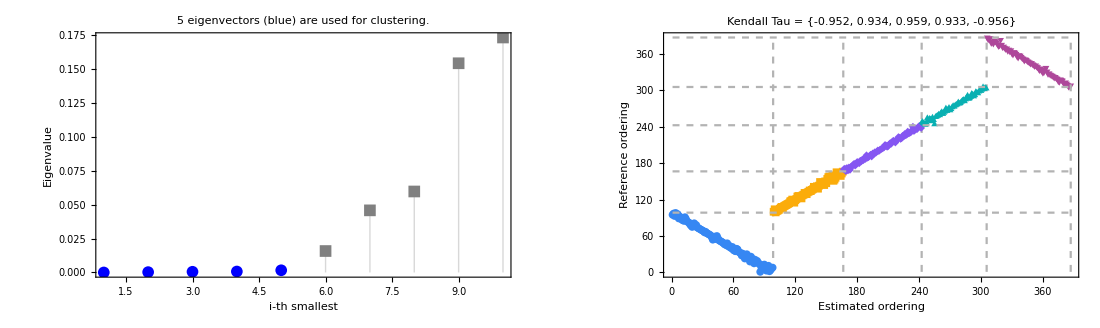

Genetic map function for initial map construction: scaled fraction = 1-Exp[-2.67 distance(M)]

Done! Finished date =Thu 30 Aug 2018 16:03:40. 	Time elapsed in total = 5.5 Seconds.

-------------------------------------------------------Refine LinkageMap-------------------------------------------------------------

magicMapRefine. Start date = Thu 30 Aug 2018 16:03:40. Outputfiles = {Example_refiningHistory.txt,Example_refinedLinkageMap.csv,Example_refinedMagicSNP.csv}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={1,2,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={4,1.22825,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={7,0.754299,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={10,0.463234,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={11,0.284484,True,True,False}

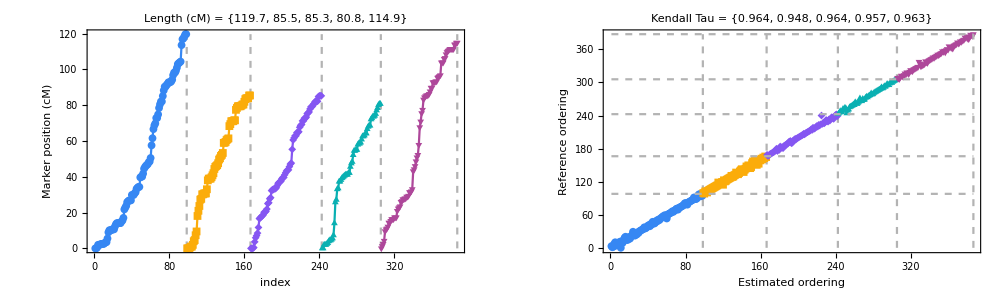

# iterations = {{15},{15},{15},{15},{15}}

Done! Finished date =Thu 30 Aug 2018 16:08:50. 	Time elapsed in total = 310.2 Seconds.

------------------------------------------------------------End---------------------------------------------------------------------

```mathematica
genodatafile=Last[datafiles]
Export[truemapfile="Example_TrueMap.csv",Transpose[Import[datafiles[[3]],Path->Directory[]][[2;;4]]]];
model=Switch[popcode,"f2","indepModel","cp","jointModel", _,"depModel"];
ngroup=5;
outputfiles=magicMap[genodatafile,model,simpedinforfile,ngroup,isFounderInbred->isfounderinbred,referenceMap->truemapfile,outputFileID->"Example"];
```

## Compare with true map

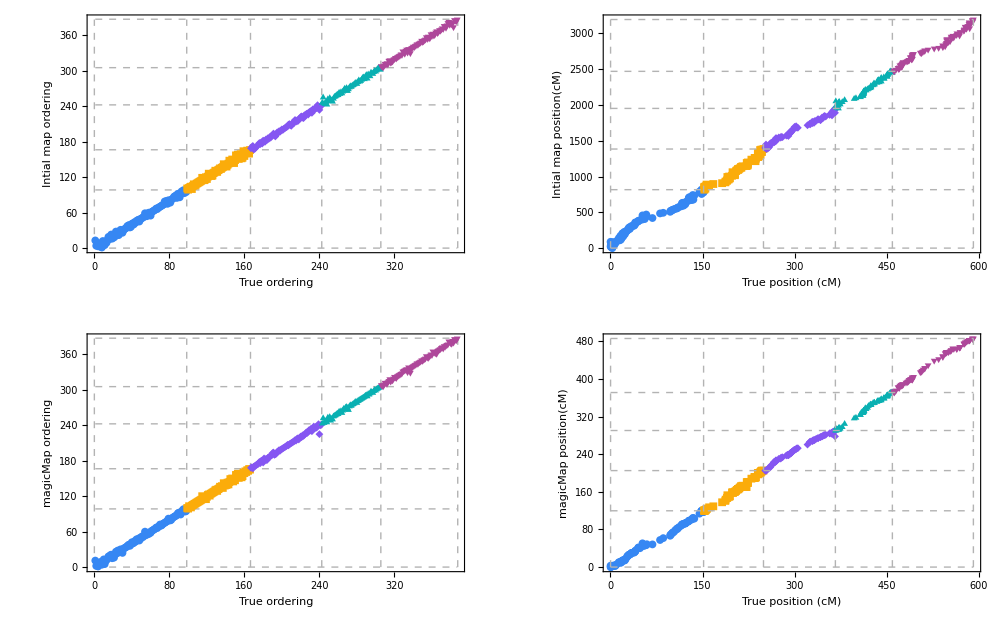

```mathematica
initmapfile="Example_initialLinkageMap.csv"; refinemapfile="Example_refinedLinkageMap.csv";
xylabel={{{"True ordering","Intial map ordering"},{"True position (cM)","Intial map position(cM)"}},{{"True ordering","magicMap ordering"},{"True position (cM)","magicMap position(cM)"}}};
gg=Table[plotMapComparison[file,truemapfile,#,Directive[Dashed,Thin,GrayLevel[0.7]],PlotMarkers->{Automatic,8}]&/@{True,False},{file,{initmapfile,refinemapfile}}];
gg=MapThread[Show[#1,Frame->True,LabelStyle->Directive[FontSize->20,Black],FrameLabel->#2]&,{gg,xylabel},2];
GraphicsGrid[gg,ImageSize->1000]
```

## Visualize heat map

```mathematica
plotHeatMapGUI["Example_pairwiseSimilarity.txt","Example_refinedLinkageMap.csv"]
```

## Refereces

Zheng, C., Boer, M. P., and Eeuwijk, F. A. 2018.  Construction of genetic linkage maps in multiparental populations. Manuscript.